## Bayes’ Classifier

P(C_k|x_1,x_2,…,x_n)=(P[x_1|C_k]P[x_2|C_k]…P[x_n|C_k]P(C_k))/(P(x_1,x_2,…,x_n))

Classifier for hand made digit, giving some digit recognition algorithm

The data set are available here with some interesting comments : http://yann.lecun.com/exdb/mnist

Recognizing digit with a Bayes’ Classifier request to compute the probability of a pixel value, of the image to analyse, to get its value in a given class
For that we need to learn this information from a data set, the data set will give us the knowledge 
We need to extract from the data set the data relative to a class, here a label representing the digit value.
For each class of label, we compute the density/distribution probability function

Notes : 

1/  This pattern In Mathematica
	f[x_] := f[x] = an Expression with x as parameter
allow to memorize the computed value of f(x) ... I use it intensively in the demo, unless we have to build a lot of storage variable... 

2/ Take care to the way Mathematica evaluate expression, delayed or not, subtle...

3/ I generate a lot of graphics, images, and the notebook can become slow, even if the computations stay fast

## Read the samples for Digit classification

### Train Data

Load training data set for image recognition

```mathematica
(* Read the file which contains the label of the digits 
You need the data file at the same level as the notebook to get it working
*)
labelsInputFile = OpenRead[NotebookDirectory[]<>"DigitSamples/train-labels.idx1-ubyte", BinaryFormat->True]
magicNumber = BinaryRead[labelsInputFile,"Integer32", ByteOrdering->1]
nbLabels = BinaryRead[labelsInputFile,"Integer32", ByteOrdering->1]
(* The label table itself *)
labels = ReadList[labelsInputFile,"Byte"];
Close[labelsInputFile];

(* Give a map values -> List of positions in the list... give us all the position of label 0,1,2,...,9 *)
GPI = PositionIndex[labels]
labels // Dimensions

(* Read the file which contains the images data of the digits, in bytes, 0 -> 255 : black to white *)
imagesInputFile = OpenRead[NotebookDirectory[]<>"DigitSamples/train-images.idx3-ubyte", BinaryFormat->True]
magicNumber = BinaryRead[imagesInputFile,"Integer32", ByteOrdering->1]
nbImages = BinaryRead[imagesInputFile,"Integer32", ByteOrdering->1]
nbRows = BinaryRead[imagesInputFile,"Integer32", ByteOrdering->1]
nbColums = BinaryRead[imagesInputFile,"Integer32", ByteOrdering->1]
(* theimages itself, a list of matrix ... dimension nbImages x nbRows x nbColums *)
DID = ReadList[imagesInputFile,Array["Byte"&,{nbRows,nbColums}]];
Close[imagesInputFile];

DID // Dimensions
(* function to retrieve the data of the given label *)
LabelData[label_] := DID[[GPI[label]]]
```

InputStream[…]

2049

60000

{60000}

InputStream[…]

2051

60000

28

28

{60000,28,28}

## How a data image look like

```mathematica
LabelData[2][[1]] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 25 | 100 | 122 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 33 | 151 | 208 | 252 | 252 | 252 | 146 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40 | 152 | 244 | 252 | 253 | 224 | 211 | 252 | 232 | 40 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 | 152 | 239 | 252 | 252 | 252 | 216 | 31 | 37 | 252 | 252 | 60 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 96 | 252 | 252 | 252 | 252 | 217 | 29 | 0 | 37 | 252 | 252 | 60 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 181 | 252 | 252 | 220 | 167 | 30 | 0 | 0 | 77 | 252 | 252 | 60 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26 | 128 | 58 | 22 | 0 | 0 | 0 | 0 | 100 | 252 | 252 | 60 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 157 | 252 | 252 | 60 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 110 | 121 | 122 | 121 | 202 | 252 | 194 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 53 | 179 | 253 | 253 | 255 | 253 | 253 | 228 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 54 | 227 | 252 | 243 | 228 | 170 | 242 | 252 | 252 | 231 | 117 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 78 | 252 | 252 | 125 | 59 | 0 | 18 | 208 | 252 | 252 | 252 | 252 | 87 | 7 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 5 | 135 | 252 | 252 | 180 | 16 | 0 | 21 | 203 | 253 | 247 | 129 | 173 | 252 | 252 | 184 | 66 | 49 | 49 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 136 | 252 | 241 | 106 | 17 | 0 | 53 | 200 | 252 | 216 | 65 | 0 | 14 | 72 | 163 | 241 | 252 | 252 | 223 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 105 | 252 | 242 | 88 | 18 | 73 | 170 | 244 | 252 | 126 | 29 | 0 | 0 | 0 | 0 | 0 | 89 | 180 | 180 | 37 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 231 | 252 | 245 | 205 | 216 | 252 | 252 | 252 | 124 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 207 | 252 | 252 | 252 | 252 | 178 | 116 | 36 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 13 | 93 | 143 | 121 | 23 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Experiment with a sub sample of the data to get the session lighter

```mathematica
(* Here we extract randomly a list of indexes *)
nbSamples = 5000;
indexesR = RandomSample[Range[Length[labels]], nbSamples];
```

```mathematica
(* Here we define new set of data from the reduced list of indexes *)
labelsR = labels[[indexesR]];
GPIR = PositionIndex[labelsR];
DIDR = DID[[indexesR]];
```

## Look At the number of each digit class

```mathematica
Length[#]& /@ GPIR
```

<|3→489,1→561,5→448,2→491,6→496,8→502,0→491,7→526,4→509,9→487|>

## Visualize a random set of the data set

```mathematica
Image[#, "Byte", ImageSize->Tiny]& /@ DIDR[[RandomSample[Range[nbSamples], 20]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Reduce the images size for the demo

```mathematica
(* function to resize image of a given label *)
ClearAll[labelDataRR] (* This is clearing all memorized values *)
labelDataRR[label_] := labelDataRR[label] = ImageData[ImageResize[Image[#, "Byte"], 14], "Byte"]& /@ DIDR[[GPIR[label]]]
```

## Show Mean of the images of a given label

Give us some data intuition, visualize the means and standard deviation of the data, very instructive

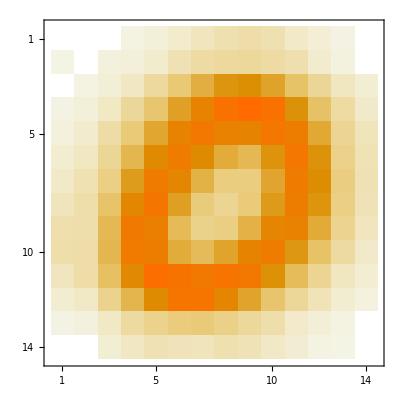
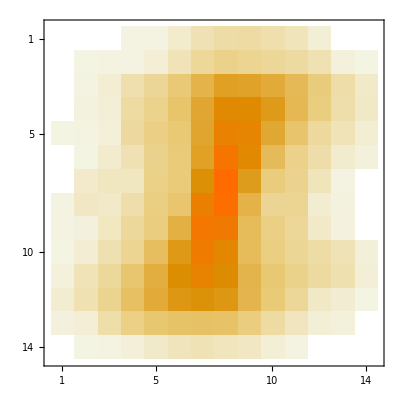
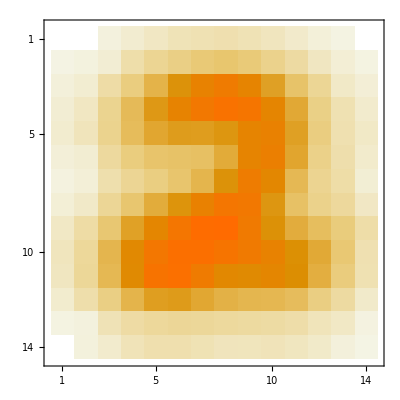
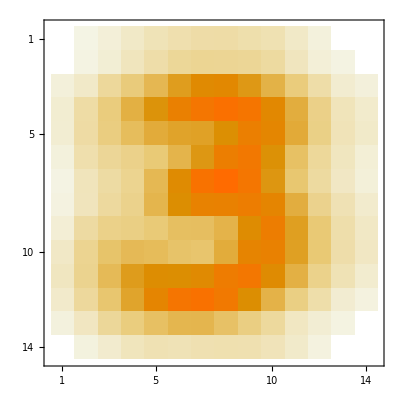
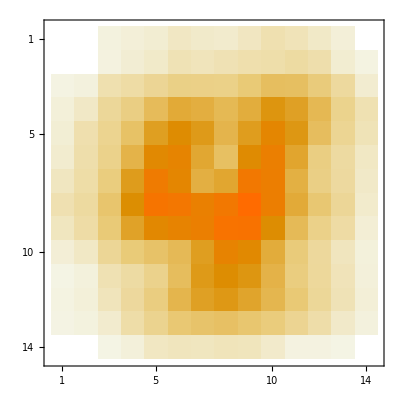
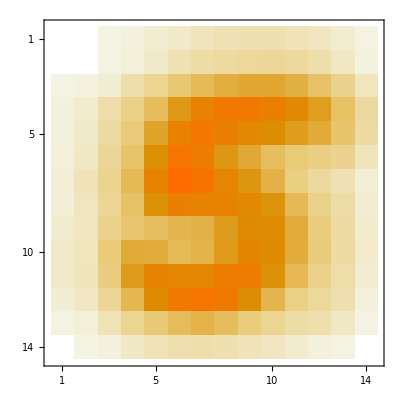
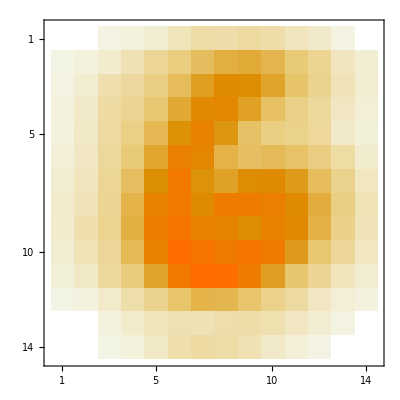
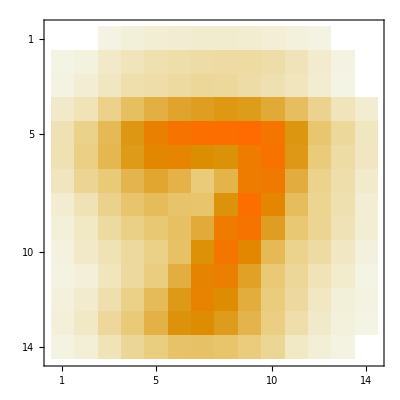

```mathematica
MatrixPlot[#]& /@ ParallelArray[(Mean[labelDataRR[#-1]])&, 10]
```

## Show Standard Deviation of the images of a given label

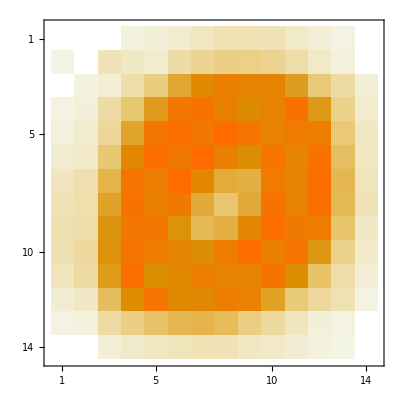
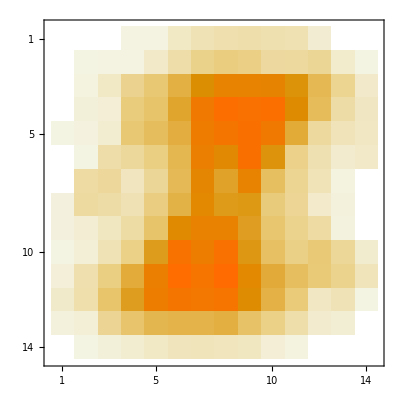
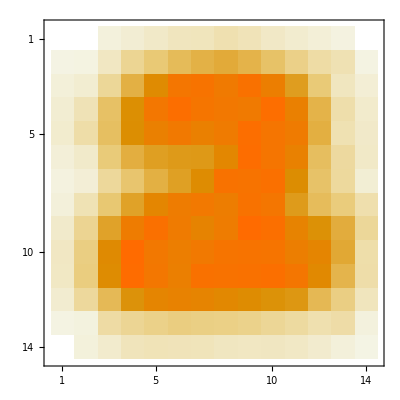
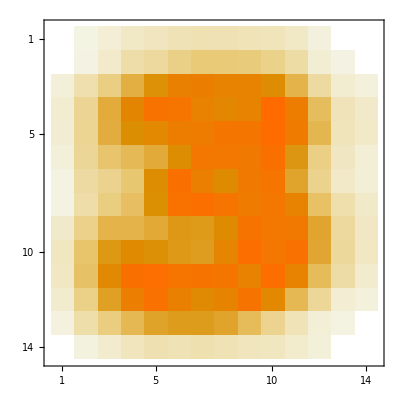
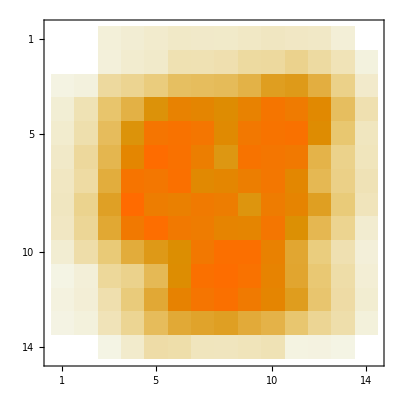
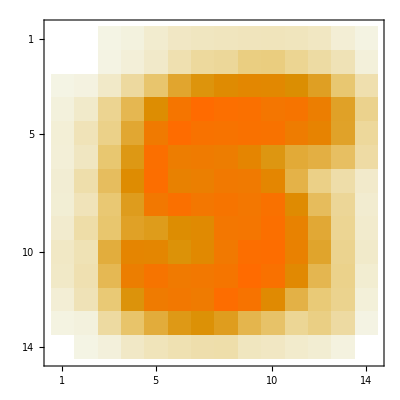
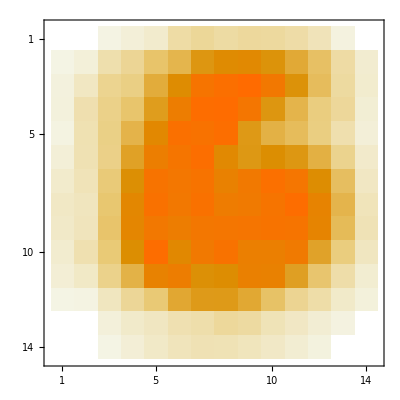
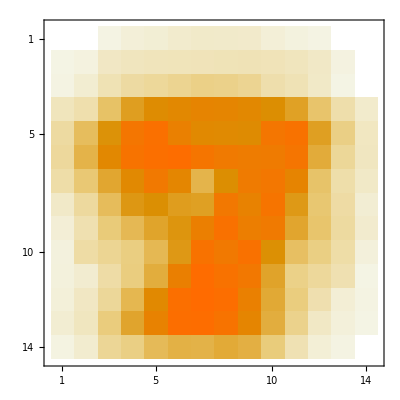

```mathematica
MatrixPlot[#]& /@ ParallelArray[(StandardDeviation[labelDataRR[#-1]])&, 10]
```

## We define the function needed to extract the features

Each pixel value or level is a feature value in our classification approach
We define the function to extract the values of a pixel, which give the feature values histogram
Then the function that create the matrix of the features values

```mathematica
ClearAll[FeatureMatrix]
featureValues[data_, i_, j_] := data[[Range[Length[data]],i,j]]  (* all the values for one specific pixel ... for the all the images*)
FeatureMatrix[data_] := FeatureMatrix[data] = Array[featureValues[data, ##]&, Drop[Dimensions[data],1]]    (* The matrix of the features , change the way to see the list of images *)
```

## We check that the matrix of the means of the features values is the same as the mean of the images

```mathematica
ll = 5;
Array[Mean[FeatureMatrix[labelDataRR[ll]][[##]]]&, Drop[Dimensions[FeatureMatrix[labelDataRR[ll]]], -1]] // MatrixPlot
```

-Graphics-

## An histogram for a feature value

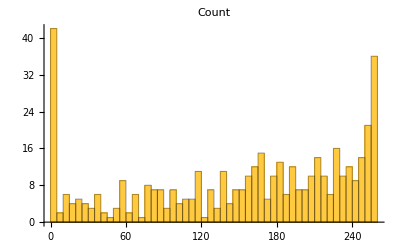
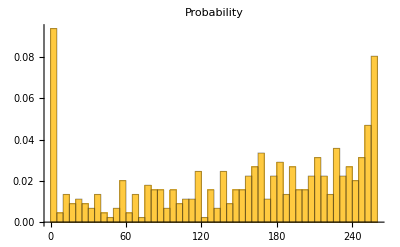
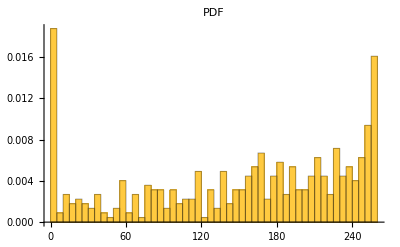

```mathematica
Table[Histogram[featureValues[labelDataRR[5],7,7],
50,h,PlotLabel->h],{h,{"Count","Probability","PDF"}}]
```

## Distribution probability function for all the feature values of all the labels

The function to know what is the probability for a given sample pixel level value in a case of a chosen category
This is the expression of the conditional probability , learnt from the data set
	P(x_(i,j)|C_k)

```mathematica
(* 
We just use one of the more obvious way to define a distribution probability density function, 
Mathematica contains a lot of different built-in probability density function,
there would be a lot of things to explore here.
*)
ClearAll[dataClassP]
dataClassP[i_, j_, label_] :=  PDF[HistogramDistribution[featureValues[labelDataRR[label], i, j]]]
```

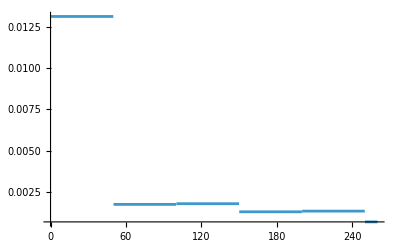
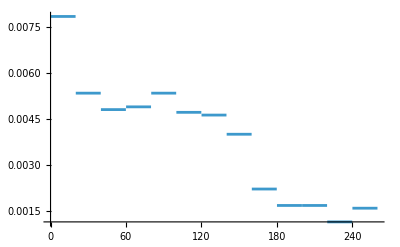
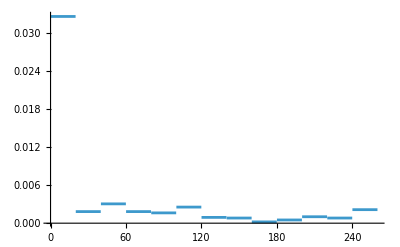
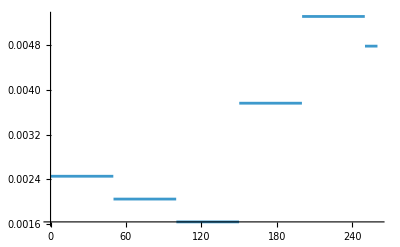
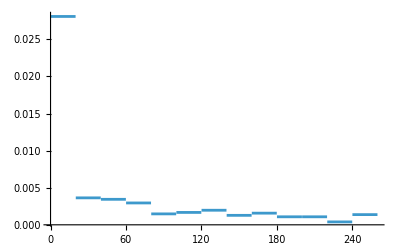
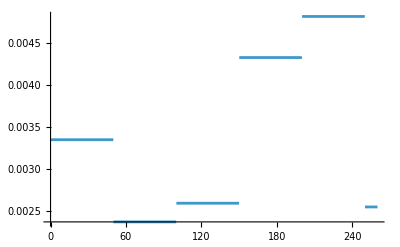
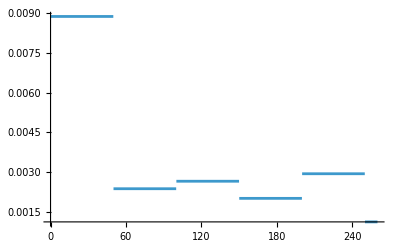
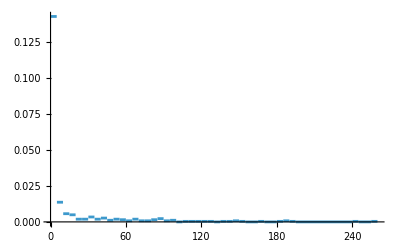

```mathematica
Parallelize[Table[Plot[dataClassP[7,7, ll][x], {x,0,260}, PlotRange->All], {ll, 0, 9}]]
```

## As an example we show the matrix of the probability distribution built from the features of the label 5

```mathematica
(* Define the function returning the matrix of probability density function of the features values of a given label*)
(* 
	The function to know what is the probability for a given sample pixel level value in a case of a chosen category
   This is the expression of the conditional probability 

	P(digit = {Subscript[x, 1,1],...,Subscript[x, 14,14]}|label = 5)
*)
ClearAll[PDFMatrix]
PDFMatrix[label_] := PDFMatrix[label] = Array[dataClassP[#1, #2, label]&, Drop[Dimensions[labelDataRR[label]], 1]]
```

```mathematica
Grid[ParallelArray[Plot[PDFMatrix[5][[#1, #2]][x], {x,0,260}, PlotRange->All]&, Dimensions[PDFMatrix[5]]]]
```

-Graphics-

## Load test data to classify a test data with the learnt probability function

### Test Data

Load test data to validate the classifier model

```mathematica
(* Read the file which contains the label of the digits of the test data set *)labelsInputFileT = OpenRead[NotebookDirectory[]<>"DigitSamples/t10k-labels.idx1-ubyte", BinaryFormat->True]
magicNumberT = BinaryRead[labelsInputFileT,"Integer32", ByteOrdering->1]
nbLabelsT = BinaryRead[labelsInputFileT,"Integer32", ByteOrdering->1]
(* The label table itself *)
labelsT = ReadList[labelsInputFileT,"Byte"];
Close[labelsInputFileT];

GPIT = PositionIndex[labelsT];
labelsT // Dimensions

(* Read the file which contains the images data of the digits, in bytes, 0 -> 255 : black to white *)
imagesInputFileT = OpenRead[NotebookDirectory[]<>"DigitSamples/t10k-images.idx3-ubyte", BinaryFormat->True]
magicNumberT = BinaryRead[imagesInputFileT,"Integer32", ByteOrdering->1]
nbImagesT = BinaryRead[imagesInputFileT,"Integer32", ByteOrdering->1]
nbRowsT = BinaryRead[imagesInputFileT,"Integer32", ByteOrdering->1]
nbColumsT = BinaryRead[imagesInputFileT,"Integer32", ByteOrdering->1]
(* The data *)
DIDT = ReadList[imagesInputFileT,Array["Byte"&,{nbRows,nbColums}]];
Close[imagesInputFileT];

DIDT // Dimensions
(* *)
LabelDataT[label_] := DIDT[[GPIT[label]]]
```

InputStream[…]

2049

10000

{10000}

InputStream[…]

2051

10000

28

28

{10000,28,28}

```mathematica
Length[#]& /@ GPIT
```

<|7→1028,2→1032,1→1135,0→980,4→982,9→1009,5→892,6→958,3→1010,8→974|>

```mathematica
Image[#, "Byte", ImageSize->Tiny]& /@ DIDT[[RandomSample[Range[nbLabelsT], 20]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Reduce the Test images size for the demo

```mathematica
(* function to resize image of a given label *)
ClearAll[labelDataTR]
labelDataTR[label_] := labelDataTR[label] = ImageData[ImageResize[Image[#, "Byte"], 14], "Byte"]& /@ DIDT[[GPIT[label]]]
```

```mathematica
Image[#, "Byte", ImageSize->Tiny]& /@ labelDataRR[2][[RandomSample[Range[Length[labelDataRR[2]]], 20]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Classifier function

All the labels have same probability, then we want to compute :

P(C_k|x_1,x_2,…,x_n)=P[x_1|C_k]P[x_2|C_k]…P[x_n|C_k]

Underflow possible ... we move in Logarithm space and will end to compare log of probability


Log(x + y) = Log(x) + Log(y)


Log[P(C_k|x_1,x_2,…,x_n)] = Log[P[x_2|C_k]] + … + Log[P[x_n|C_k]]

```mathematica
(* We don' t let a value to be 0 *)
epsilon = 10^-4;
```

## Apply PDF matrix to a data test digit image

```mathematica
(* Apply density function to every pxel value *)
MatrixCompMap[fm_, vm_] := Array[fm[[##]][vm[[##]]]&, Dimensions[vm]]
```

## Apply the probability density function to each pixel values for all label

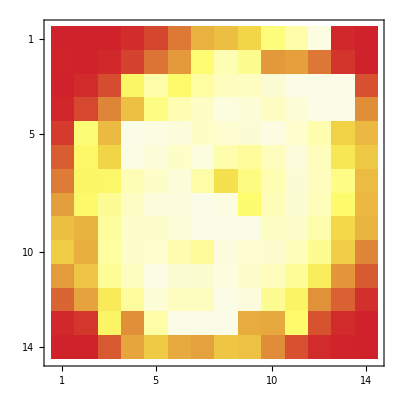
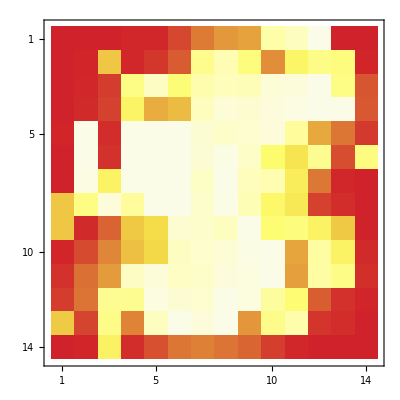
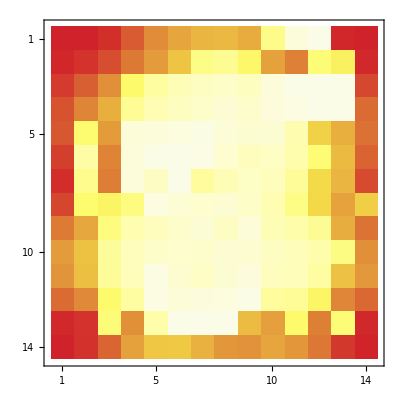
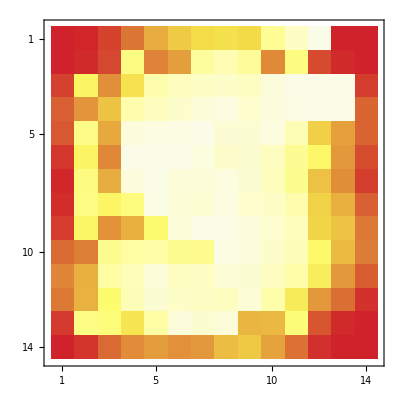
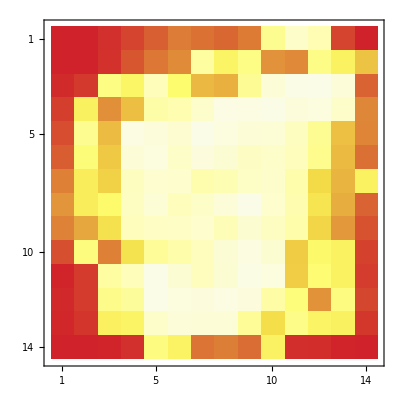
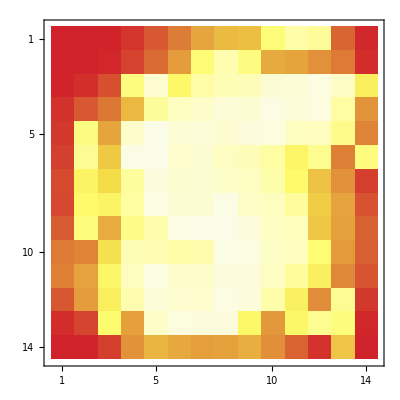
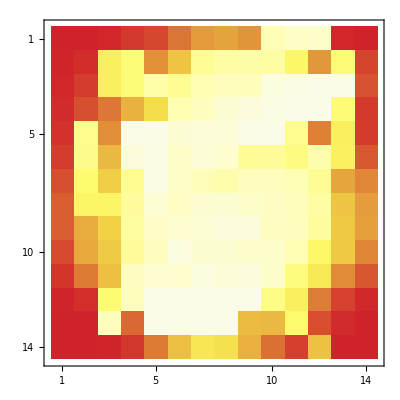
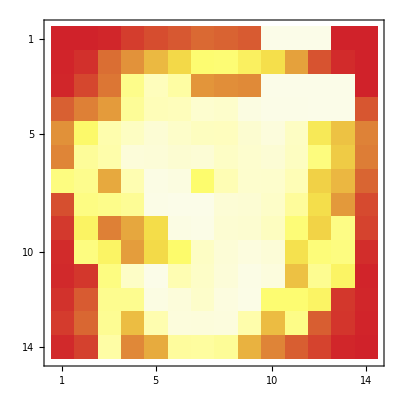

```mathematica
Parallelize[Table[MatrixCompMap[PDFMatrix[ll], labelDataTR[5][[10]]] // MatrixPlot[#, ColorFunction->"TemperatureMap"]&, {ll, 0, 9}]]
```

## Using Log

```mathematica
(* Compute the matrix of the P(Subscript[x, i]|Ck) *)
logMatrixCompMap[fm_, vm_] := ParallelArray[Log[Max[fm[[#1,#2]][vm[[#1, #2]]], epsilon]]&, Dimensions[vm]]
```

## Apply the probability density function to each pixel values for all label, applying the Log function Very interesting here, the recognized digit is one we can recognize visually

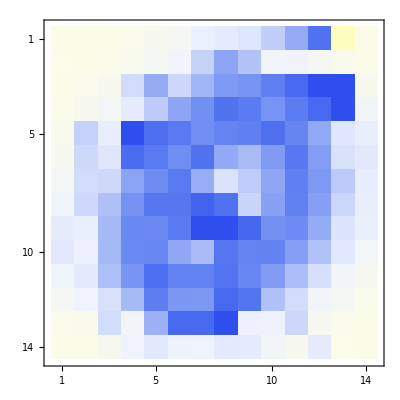
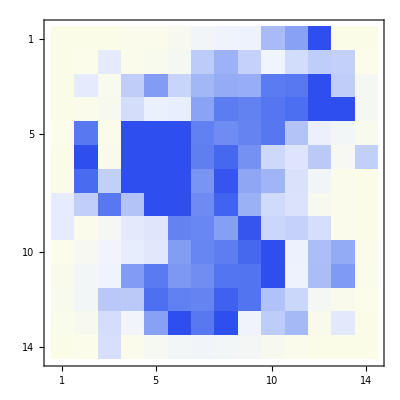
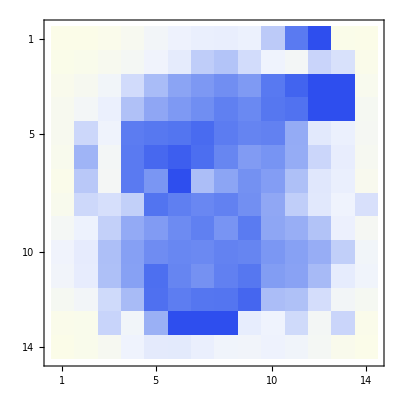
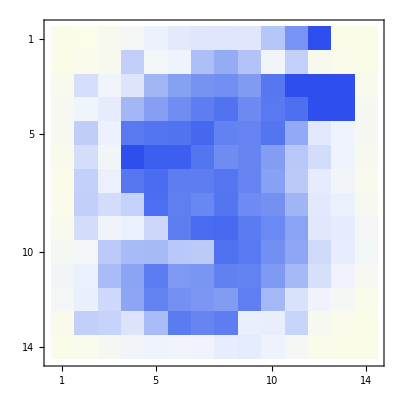
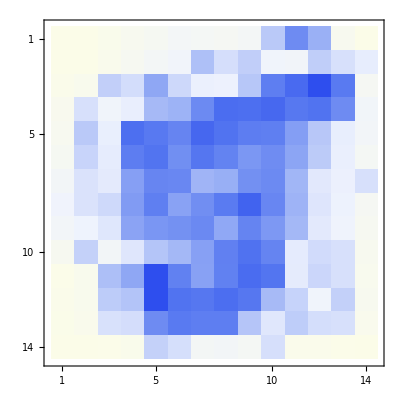
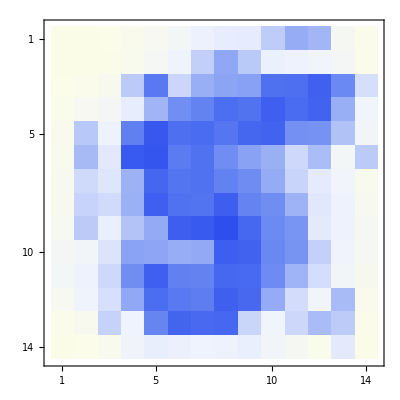
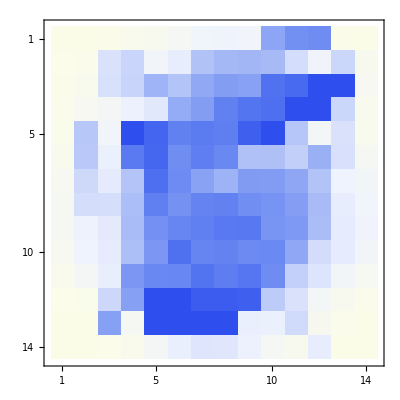
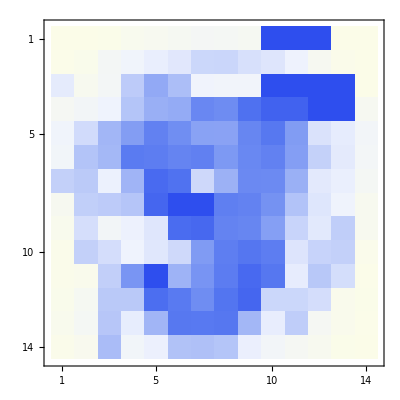

```mathematica
Table[logMatrixCompMap[PDFMatrix[ll], labelDataTR[5][[10]]] // MatrixPlot[#, ColorFunction->"TemperatureMap"]&, {ll, 0, 9}]
```

## We sum the Log values and classify the digit by comparing probability values found for each Class

## The function which compute P(Ck|x_1,x_(2,...,x_n))

```mathematica
logClassProbM[label_, digit_] := Fold[#1+#2&, Flatten[Array[Log[Max[PDFMatrix[label][[#1,#2]][digit[[#1, #2]]], epsilon]]&, Dimensions[digit]]]]
```

## We apply it to all test data of the label 5 : labelDataTR[5] And get the most probable recognized digit for each test data

```mathematica
Parallelize[Table[Array[logClassProbM[#-1, labelDataTR[5][[i]]]&, 10] // Ordering[#, -1]-1&, {i, 1, Length[labelDataTR[5]]}]]
```

{{4},{3},{5},{8},{5},{3},{1},{7},{3},{5},{5},{3},{8},{3},{5},{5},{3},{9},{1},{3},{3},{5},{7},{5},{3},{5},{1},{5},{6},{8},{3},{8},{6},{5},{3},{0},{5},{5},{3},{5},{5},{3},{0},{3},{5},{7},{8},{6},{9},{8},{5},{8},{5},{8},{5},{3},{9},{3},{7},{3},{3},{3},{7},{8},{8},{5},{6},{3},{3},{8},{3},{8},{3},{4},{8},{5},{5},{1},{8},{5},{5},{5},{5},{7},{6},{5},{8},{3},{9},{8},{5},{8},{5},{7},{5},{8},{3},{0},{5},{9},{5},{1},{3},{3},{5},{9},{5},{9},{6},{3},{8},{6},{8},{9},{5},{5},{9},{7},{3},{3},{3},{5},{8},{8},{8},{3},{5},{8},{4},{5},{5},{3},{9},{5},{7},{0},{5},{8},{5},{0},{5},{5},{7},{5},{5},{1},{5},{5},{5},{5},{7},{5},{1},{5},{2},{8},{3},{3},{5},{5},{8},{5},{5},{3},{3},{8},{1},{3},{3},{3},{5},{8},{3},{5},{9},{4},{5},{3},{9},{9},{8},{5},{5},{5},{5},{6},{4},{9},{5},{5},{5},{3},{5},{5},{8},{9},{4},{8},{3},{3},{3},{5},{3},{6},{8},{5},{3},{3},{8},{7},{3},{7},{5},{6},{3},{3},{9},{3},{9},{0},{5},{5},{5},{1},{3},{0},{3},{8},{5},{3},{5},{3},{3},{8},{3},{8},{8},{5},{3},{5},{8},{3},{8},{5},{3},{8},{5},{5},{6},{4},{7},{3},{1},{8},{1},{5},{5},{8},{9},{8},{4},{3},{5},{3},{3},{5},{3},{8},{5},{1},{9},{9},{8},{8},{1},{5},{8},{3},{1},{1},{3},{6},{1},{5},{5},{7},{8},{3},{8},{3},{1},{5},{5},{9},{5},{8},{9},{3},{3},{8},{5},{5},{3},{0},{5},{3},{5},{7},{1},{7},{3},{3},{5},{3},{3},{5},{8},{5},{5},{6},{8},{8},{4},{6},{3},{5},{8},{5},{9},{5},{5},{7},{9},{4},{7},{1},{5},{3},{3},{9},{5},{8},{3},{9},{8},{8},{5},{5},{9},{9},{5},{5},{5},{8},{3},{5},{5},{5},{6},{9},{3},{5},{5},{7},{3},{3},{3},{7},{8},{5},{3},{8},{3},{3},{5},{9},{8},{5},{1},{5},{1},{7},{5},{1},{1},{5},{3},{5},{5},{9},{5},{5},{5},{0},{5},{3},{3},{8},{1},{5},{8},{1},{9},{7},{6},{3},{3},{9},{8},{8},{3},{5},{6},{6},{5},{3},{3},{3},{3},{5},{5},{5},{8},{5},{0},{3},{1},{1},{5},{5},{8},{3},{3},{5},{9},{4},{5},{8},{3},{5},{5},{8},{8},{7},{6},{5},{3},{3},{0},{5},{8},{8},{8},{7},{3},{3},{8},{5},{8},{8},{5},{5},{6},{5},{5},{5},{5},{5},{5},{5},{5},{5},{0},{5},{5},{5},{1},{5},{5},{5},{3},{3},{5},{8},{5},{5},{5},{3},{3},{5},{5},{5},{5},{5},{5},{5},{5},{5},{3},{3},{8},{0},{0},{3},{5},{5},{5},{6},{5},{5},{5},{5},{5},{3},{5},{8},{8},{5},{8},{3},{6},{5},{6},{6},{5},{8},{3},{3},{5},{0},{3},{3},{3},{3},{3},{6},{5},{2},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{3},{5},{5},{8},{5},{5},{8},{5},{5},{5},{5},{8},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{2},{5},{5},{5},{6},{0},{6},{4},{3},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{8},{3},{5},{5},{6},{5},{1},{5},{5},{8},{8},{0},{1},{1},{8},{3},{6},{5},{3},{5},{3},{8},{3},{8},{6},{9},{5},{9},{5},{5},{5},{0},{5},{5},{6},{5},{5},{3},{5},{5},{1},{5},{5},{1},{5},{5},{5},{5},{5},{7},{5},{5},{5},{6},{5},{8},{8},{1},{3},{8},{8},{8},{8},{8},{5},{5},{5},{5},{3},{5},{3},{5},{0},{1},{1},{1},{5},{0},{3},{0},{5},{8},{4},{1},{3},{5},{5},{1},{5},{3},{3},{3},{6},{5},{3},{3},{8},{8},{3},{3},{3},{8},{5},{5},{0},{0},{5},{2},{5},{5},{8},{8},{4},{0},{4},{9},{1},{4},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{8},{8},{8},{8},{8},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{1},{5},{5},{5},{5},{5},{5},{4},{8},{8},{8},{7},{5},{0},{3},{5},{5},{5},{0},{5},{0},{6},{5},{5},{0},{3},{3},{5},{3},{3},{0},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{8},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{5},{8},{5},{5},{5},{8},{1},{5},{3},{0},{5},{5},{5},{5},{8},{4},{5},{5},{8},{5},{5},{5},{8},{5},{7},{5},{5},{5},{5},{7},{8},{8},{8},{5},{8},{8},{5},{9},{5},{3},{5},{3},{0},{5},{5},{5},{5},{8},{5},{4},{8},{5},{5},{5},{5},{8},{9},{5},{5},{1},{5},{5},{5},{5},{8},{5},{5},{8},{0},{6},{5},{5},{1},{0},{4},{5},{1},{8},{1},{1},{1},{8},{1},{1},{1},{6},{2},{6},{8},{8}}

## We apply it for all the test data and for all the label To get the success rate of the classification

```mathematica
(* The simple function which do the calculus for a given label *)
TestDataSet[label_] :=
Parallelize[Table[Array[logClassProbM[#-1, labelDataTR[label][[i]]]&, 10] // Ordering[#, -1]-1&, {i, 1, Length[labelDataTR[label]]}]]// Flatten // PositionIndex // Map[Length[#]&, #]&
```

Apply it to label 5

```mathematica
TestDataSet[5]
```

<|4→20,3→167,5→377,8→134,1→51,7→29,9→39,6→37,0→33,2→5|>

Apply it to label 6

```mathematica
TestDataSet[6]
```

<|6→854,5→17,0→29,1→27,4→10,8→7,2→9,9→3,7→1,3→1|>

## Conclusion

We can see that the result depend on the label here, keep in mind that we didn’t take all the learning data in account, and that we have reduced the size of the images.

We could have to explore other kind of probability density function computed from the learning data set

But at the end for a very naive way to classify, we get interesting results.

And we can see that our features are not independent, the positions of adjacent pixels seem to follow a difficult to grasp law